Copyright Steve Flammia 2018–2020

## Stabilizer generators for n-qubit MUBs

This function computes the structure constants of the finite field GF[q].

```mathematica
<<FiniteFields`
$DistributedContexts="FiniteFields`";
GFStructureConstants[q_,n_]:=Module[{bs,x,α,sc},
PowerListQ[GF[q]]=True; 
(* bs⟦j⟧ is the j^th basis element *)
bs=Map[GF[q][#]&,IdentityMatrix[n]];
α[m_,j_,k_]:=Coefficient[ElementToPolynomial[FieldExp[GF[q],FieldInd[bs⟦j⟧]+FieldInd[bs⟦k⟧]],x],x,m-1];
sc=Table[α[m,j,k],{m,n},{j,n},{k,n}];
Return[sc];
];
```

The stabilizers can be written as binary vectors of length 2n, and we have the following way to list them all. It’s pretty fast and runs in a few seconds for n=15. The second form constructs the constituent generators as Pauli matrices. The last one computes the kth element of the jth MUB in a self-consistent way with respect to the phases by multiplying out the generators.

```mathematica
MUBvecs[n_]:=Module[{r,α,S},
α=GFStructureConstants[2^n,n];
S=Join[Table[ArrayFlatten[{{IdentityMatrix[n],Mod[(IntegerDigits[r,2,n].α),2]}}],{r,2^n}],{ArrayFlatten[{{0 IdentityMatrix[n],IdentityMatrix[n]}}]}];
Return[S];
];

(* Requires the definition of P[] below. *)
MUBgens[n_,k_]:=P[FromDigits[#,2],n]&/@(MUBvecs[n]⟦k⟧);

(* The kth element of the jth MUB. *)
MUBelements[n_,j_,k_]:=Dot@@Thread[MatrixPower[MUBgens[n,j],IntegerDigits[k,2,n]]]
```

The cth rank-1 density operator for the jth MUB.

```mathematica
MUBstate[n_,c_,j_]:=1/2^n Sum[(-1)^BitDot[c,k] MUBelements[n,j,k],{k,2^n}]
```

We might need to label all of the MUBs in a self-consistent way, up to the phases. This returns the integer labels of each MUB.

```mathematica
MUBints[n_]:=(Mod[Table[IntegerDigits[k,2,n],{k,0,2^n-1}].#,2]&/@MUBvecs[n]).Table[2^(2n-1-k),{k,0,2n-1}];
```

## Random probability distributions and Paulis

#### Random Numbers

```mathematica
(*Generates a normally distributed random number with mean μ and standard deviation σ.  There is also A matrix version. The dimensions of the matrix are specified by the list L or the integer n.*)
RandomNormal[μ_:0,σ_:1]:=RandomReal[NormalDistribution[μ,σ]]
RandomNormal[L_List]:=RandomReal[NormalDistribution[0,1],L]
RandomNormal[n_Integer]:=RandomReal[NormalDistribution[0,1],{n}]
RandomNormal[L_List,μ_,σ_]:=RandomReal[NormalDistribution[μ,σ],L]
RandomNormal[n_Integer,μ_,σ_]:=RandomReal[NormalDistribution[μ,σ],{n}]

(*Complex version, normalized to have unit variance.*)
RandomComplexNormal[x___]:=1/(√2)(RandomNormal[x]+ⅈ RandomNormal[x])
```

We project onto the closest point in Euclidean distance to the simplex to get an actual probability distribution:

#### Simplices

```mathematica
(* This function implements a simple algorithm to project a vector p onto the probability simplex with minimal distortion in Euclidean distance. Faster algorithms exist, but this is very simple to code. The worst case runtime is O(n^2), the average case is O(n log(n)) due to the use of sorting. *)
ProjectSimplex[p_]:=Module[{n=Length[p],u,U,K,k,τ,q},
u=Sort[p,Greater];
U=Accumulate[u];
K=Max[Table[If[(U⟦k⟧-1)/k<u⟦k⟧,k,0],{k,n}]];
τ=(U⟦K⟧-1)/K;
q=(Max[#-τ,0]&/@p);
Return[q];
];

(*Generates a uniform sample from the d dimensional simplex.*)
RandomSimplex[d_]:=Differences[Join[{0},Sort[Table[RandomReal[],{d-1}]],{1}]];
```

#### Random Matrices and States

```mathematica
(*Generates a random dxd Hermetian matrix.*)
RandomHermitian[d_Integer]:=Module[{H,G,j},
H=Table[If[j<k,RandomComplexNormal[]/√2,0],{j,d},{k,d}];
G=DiagonalMatrix[RandomNormal[d]];
H=H+H†+G;
H
]

(*Generating Haar random unitaries via QR decomposition.*)
(*Generates a Haar random dxd unitary matrix.*)
RandomUnitary[d_Integer]:=Module[{A,Q,R,diag,y,U},
A=RandomComplexNormal[{d,d}];
{Q,R}=QRDecomposition[A];
diag=Diagonal[R];
y=diag/Abs[diag];
U=Q.DiagonalMatrix[y]
]

(*Generates a Haar-random dxd pure state vector.*)
RandomState[d_Integer]:=Module[{v,ψ},
v=RandomComplexNormal[d];
ψ=v/Norm[v]
]

(*Generates a random dxd density operator with rank k.  When k=1, you get a Haar-random pure state.  When k=d, you get a Hilbert-Schmidt measure mixed state.*)
RandomState[d_Integer,k_Integer]:=Module[{A,M,ρ},
A=RandomComplexNormal[{d,k}];
M=A.A†;
ρ=M/Tr[M]
]

(*Random state drawn from Bures measure.*)
RandomBures[d_Integer]:=Module[{A,U,X,M,ρ},
A=RandomComplexNormal[{d,d}];
U=RandomUnitary[d];
X=A+U.A;
M=X.X†;
ρ=M/Tr[M]
]

(* Haar-random projector of rank r on ℂ^d *)
RandomProjector[r_Integer,d_Integer]:=Module[{M},
M=RandomUnitary[d];
M=M⟦1;;r,All⟧;
M†.M
]
```

#### Paulis

```mathematica
P[b_List]:=Module[{n=Length[b]/2,x,z,X,Z,T},
{x,z}=Partition[b,n];
{X,Z}=FromDigits[#,2]&/@{x,z};
T=(-ⅈ)^(x.z) SparseArray[Table[{BitXor[X,c]+1,c+1}->(-1)^(z.IntegerDigits[c,2,n]),{c,0,2^n-1}]];
Return[T];
];

P[b_Integer,n_Integer]:=P[IntegerDigits[b,2,2 n]]

(* This expands a Hermitian matrix as a vector in the Pauli basis *)
Pb[M_]:=Module[{n=Log2[Length[M]]},
Return[Table[Re[Tr[(P[k,n]/(√(2^n))).M]],{k,0,4^n-1}]];
];
```

```mathematica
(* Converts the arguments to bit strings and computes the mod 2 inner product. *)
BitDot[a_,b_]:=Mod[Tr[IntegerDigits[BitAnd[a,b],2]],2];
```

## Simulation functions

```mathematica
(*Generate a probability distribution on 4^n outcomes where the first element is 1-err. If sparse is a positive interger, then it adds a smaller random simplex with sparse elements as an (q,1-q) mixture to the random one.*)
GenerateP[n_,err_,sparse_:0,q_:1/2]:=Module[{d=2^n,p},
If[sparse==0,
p=err RandomSimplex[d^2-1];,
p=q err RandomSimplex[d^2-1]+(1-q)err (RandomSample[Join[RandomSimplex[sparse],ConstantArray[0,{d^2-1-sparse}]]]);
];
Return[Join[{1-err},p]];
];

(* Generate independent depolarizing noise on n qubits with error probability err, plus a small random perturbation that sums to zero, then project back. The second version handles perturbations of any Pauli channel.*)
GenerateAlmostIndependentP[n_,err_,perturb_]:=Module[{p},
p=Flatten[KroneckerProduct@@ConstantArray[{1-err,err/3,err/3,err/3},n]];
p=p+perturb (RandomSimplex[4^n]-1/4^n); 
p=ProjectSimplex[p];
Return[p];
];
(*Here the error is a vector of Pauli errors.*)
GenerateAlmostIndependentP[n_,err_List,perturb_]:=Module[{p},
p=Flatten[KroneckerProduct@@ConstantArray[err,n]];
p=p+perturb (RandomSimplex[4^n]-1/4^n); 
p=ProjectSimplex[p];
Return[p];
];


H[d_]:=RandomHermitian[d];
U[ϵ_,M_]:=MatrixExp[ⅈ ϵ M/Norm[M]];
(*Define the W transform as a fast transform, instead of a matrix.*)
W[M_]:=√Length[M] DiscreteHadamardTransform[M,Method->"BitComplement"];
```

This takes a probability distribution p and a SPAM strength spam, as well as a precision ϵ and a confidence δ, and returns an estimate of p using the full Pauli noise reconstruction algorithm.

```mathematica
RunCB[p_,spam_,ϵ_,δ_,PrintFlag_:False]:=Module[{d=Sqrt[Length[p]],n,f,fest,U1,U2,rr,ee,Δ,log2mmax,RBprobs,estRBprobs,RBF,T,j,F,ratioest,pestInit},
n=Log2[d];
f=W[p];
fest=ConstantArray[0,{d^2}];
(*Create spam and the RB probabilities.*)
U1=U[spam,H[d]];
U2=U[spam,H[d]];
rr[n_,j_]:=rr[n,j]=Pb[U1.MUBstate[n,0,j].U1†];
ee[n_,j_]:=ee[n,j]=Table[Pb[U2.MUBstate[n,c,j].U2†],{c,0,2^n-1}];
Δ=(1-Max[Rest[f]]);
log2mmax=Ceiling[Log2[1/Δ]]+1;
RBprobs[n_,j_]:=RBprobs[n,j]=Table[ee[n,j].(f^(2^k)*rr[n,j]),{k,0,log2mmax}];
estRBprobs[n_,j_,T_]:=Map[1/T RandomVariate[PoissonDistribution[T #]]&,RBprobs[n,j],{2}];
RBF[n_,j_,T_]:=(W/@estRBprobs[n,j,T])ᵀ;
(* Now run the RBprobs function so that it evaluates on all the inputs. *)
Do[RBprobs[n,j];,{j,d+1}];
(*Print["Elapsed Time: ",AbsoluteTiming[Do[RBprobs[n,j];,{j,d+1}];]⟦1⟧," seconds"];
*)
(*Now loop over all MUBs and estimate.*)
T=Floor[Log[δ^-1 2^(log2mmax+1) d^2 ]/((1+ϵ)Log[1+ϵ]-ϵ)];
If[PrintFlag,Print["T = ",T]];
For[j=1,j≤d+1,j++,
F=RBF[n,j,T];
ratioest=(F⟦#⟦1⟧,#⟦2⟧⟧/F⟦#⟦1⟧,1⟧)^(1.0/(2^(#⟦2⟧-1)-1))&/@({Range[d],(FirstPosition[Thread[#<1/3 First[#]],True,{Length[#]}]⟦1⟧&/@F)}ᵀ);
(*Here are the associated channel fidelities.*)
fest⟦MUBints[n]⟦j⟧+1⟧=ratioest;
];
(*Normalize *)
fest⟦1⟧=1;
(*Compute the probability estimates.*) 
pestInit=W[fest]/d^2;
(*Print["T = ",T];*)
Return[ProjectSimplex[pestInit]];
];
```

## Plots for few qubits

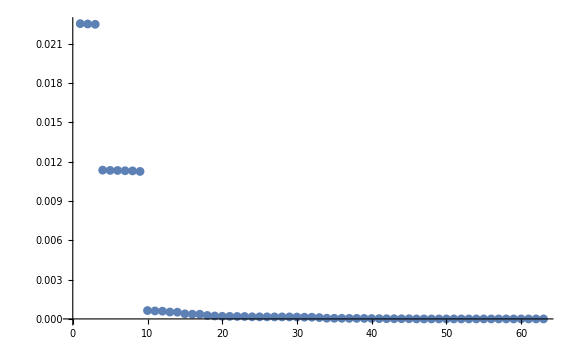

T = 962131

```mathematica
n=3;
d=2^n;
err=0.05;
(*numberSparse=5;
p=GenerateP[n,err,numberSparse];*)
perturb=0.008;
(*Almost independent depolarizing noise*)
p=GenerateAlmostIndependentP[n,err,perturb];
(*Almost independent biased noise.*)
errvec={1-err,1/4 err,1/4 err,2/4 err};
p=GenerateAlmostIndependentP[n,errvec,perturb];
ListPlot[Rest[Sort[p,Greater]],PlotRange->All]

ϵ=.005; δ=0.05; spam=0.1;
pest=RunCB[p,spam,ϵ,δ,True];
f=W[p]; fest=W[pest];
```

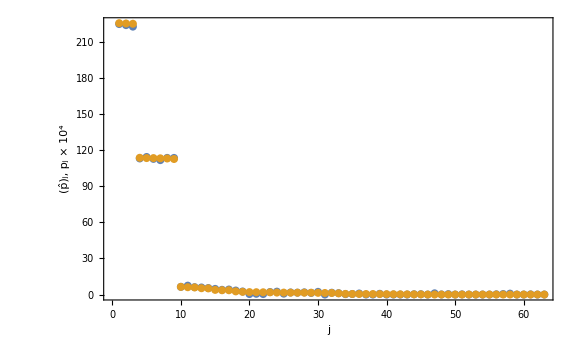

```mathematica
ord=Ordering[Rest[p],Length[p]-1,Greater];
SetOptions[ListPlot,ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->PointSize[0.01]];
fig1=ListPlot[{10^4 Rest[pest]⟦ord⟧,10^4 Rest[Sort[p,Greater]]},PlotRange->All,FrameLabel->{"j","(p̂)_j, p_j × 10^4"},Frame->True,Epilog->Inset[ListPlot[10^3/errprob Sort[Abs[pest-p],Greater],PlotRange->All,FrameLabel->{"j","(|OverHat[p_j]-p_j|)/(1-p_0) × 10^3"},ImageSize->Medium,Frame->True],ImageScaled[{.66,0.6}]]]
```

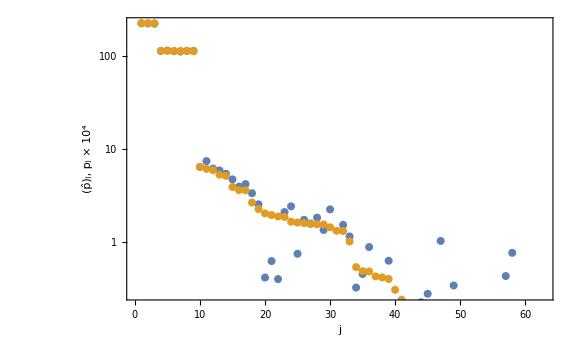

```mathematica
SetOptions[ListLogPlot,ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->PointSize[0.01]];
fig1=ListLogPlot[{10^4 Rest[pest]⟦ord⟧,10^4 Rest[Sort[p,Greater]]},PlotRange->{0,All},FrameLabel->{"j","(p̂)_j, p_j × 10^4"},Frame->True,Epilog->Inset[ListPlot[10^3/errprob Sort[Abs[pest-p],Greater],PlotRange->{0,All},FrameLabel->{"j","(|OverHat[p_j]-p_j|)/(1-p_0) × 10^3"},ImageSize->Scaled[250],Frame->True],ImageScaled[{.35,0.35}]]]
```

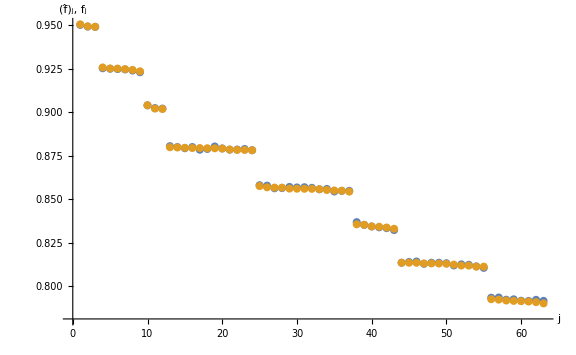

```mathematica
ordf=Ordering[Rest[f],Length[f]-1,Greater];
SetOptions[ListPlot,ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->PointSize[0.01]];
fig1=ListPlot[{Rest[fest]⟦ordf⟧,Rest[Sort[f,Greater]]},PlotRange->All,AxesLabel->{"j","(f̂)_j, f_j"},Epilog->Inset[ListPlot[10^2/errprob Sort[Abs[fest-f],Greater],PlotRange->{0,All},FrameLabel->{"j","(|OverHat[f_j]-f_j|)/(1-p_0) × 10^2"},ImageSize->Scaled[250],Frame->True],ImageScaled[{.76,0.70}]]]
```

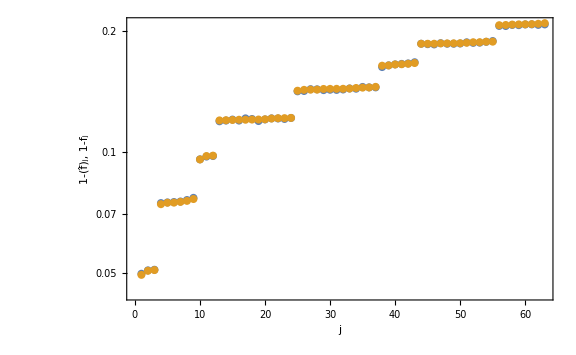

```mathematica
SetOptions[ListLogPlot,ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->PointSize[0.01]];
fig1=ListLogPlot[{1-Rest[fest]⟦ordf⟧,1-Rest[Sort[f,Greater]]},PlotRange->All,FrameLabel->{"j","1-(f̂)_j, 1-f_j"},Frame->True,Epilog->Inset[ListPlot[10^2/errprob Sort[Abs[fest-f],Greater],PlotRange->{0,All},FrameLabel->{"j","(|OverHat[f_j]-f_j|)/(1-p_0) × 10^2"},ImageSize->Scaled[250],Frame->True],ImageScaled[{.76,0.35}]]]
```

## 1D-chain Markov network reconstruction

The goal of this section is to get the code working on nearest-neighbor chains.

An estimate of a chordal (triangulated) undirected model is given by taking the empirical marginals on each clique and the empirical marginals on each intersection of clique pairs and taking the ratio of the products, (Π_C p̂(x_C))/(Π_I p̂(x_I)).

### Function definitions

```mathematica
(*The brute-force trace distance*)
TD[x_?VectorQ]:=1/2 Tr[Abs[x]];
(* Given a bipartite probability distribution p as a matrix, return the mutual information. *)
MutualInformation[p_?MatrixQ]:= Max[{0.0,Total[p Log[p / Outer[Times,Total[p,{2}],Total[p,{1}]]],2]}]

(*This computes the probability of the integer x (as a 4-ary string) given the normalized clique potentials ϕ. *)
Pr[x_?VectorQ,ϕ_]:=Product[ϕ⟦j,FromDigits[x⟦{j,j+1}⟧,4]+1⟧,{j,Length[x]-1}];
Pr[x_Integer,ϕ_]:=Pr[IntegerDigits[x,4,Length[ϕ]+1],ϕ]

(*This takes a list of marginal probability distributions on overlapping sites on a chain and returns a list of clique potentials in a standard form. The probabilities are normalized after this transformation. *)
Fix[ϕ_]:=Module[{L=Length[ϕ]+1,margϕ,newϕ=ϕ},
margϕ=Most[Total/@Partition[#,4]&/@ϕ];
Do[newϕ⟦j⟧=Flatten[(Partition[ϕ⟦j⟧,4]/margϕ⟦j⟧)ᵀ];,{j,L-2}];
Return[newϕ];
];

(*Return a marginal probability distribution on the set of indices s given the normalized clique potentials ϕ. It assumes only a pair of neighboring indicies at the moment. *)
NNMarginal[s_,ϕ_]:=Module[{L=Length[ϕ]+1,M,R,j},
M=Partition[#,4]&/@ϕ;
R=ConstantArray[1,{4}];
For[j=L-1,j≥Max[s],j--,
R=M⟦j⟧.R;
];
Return[Flatten[(M⟦Min[s]⟧ᵀ R)ᵀ]];
];

(* Nearest Neighbor Bhattacharyya Coefficient *)
BhattacharyyaCoefficient[ϕ_,ϕest_]:=Module[{A=Sqrt[ϕ] Sqrt[ϕest],B,j,t={1,1,1,1}},
B=Partition[#,4]&/@A;
For[j=Length[B],j≥1,j--,
t=B⟦j⟧.t;
];
Return[{1,1,1,1}.t];
];

(* Compute the Hellinger distance *)
HellingerDistance[ϕ_,ϕest_]:=√(1-BhattacharyyaCoefficient[ϕ,ϕest]);

(* Take 1 sample (or k) from the probability distribution specified by ϕ. *)
ChainSample[ϕ_]:=Module[{L=Length[ϕ]+1,samp,M1,M2,j,condmarg},
samp=ConstantArray[0,L];
M2=Table[Partition[NNMarginal[{1,2}+s,ϕ],4],{s,0,L-2}];
M1=Total[#,{1}]&/@M2;
M1=Prepend[M1,Total[M2⟦1⟧,{2}]];
samp⟦1⟧=RandomChoice[M1⟦1⟧->Range[4]];
For[j=1,j<L,j++,
condmarg=M2⟦j,samp⟦j⟧,All⟧/M1⟦j,samp⟦j⟧⟧; (*Conditional marginal*)
samp⟦j+1⟧=RandomChoice[condmarg->Range[4]];
];
Return[samp-1];
];

(* Marginal probability of an error on pairs of sites. *)
Wt[ϕ_]:=Module[{L=Length[ϕ]+1,M2},
M2=Table[Partition[NNMarginal[{1,2}+s,ϕ],4],{s,0,L-2}];
Return[{{#⟦1,1⟧,Total[#⟦1,2;;4⟧]},{Total[#⟦2;;4,1⟧],Total[#⟦2;;4,2;;4⟧,2]}}&/@M2];
];
(* Correlation between neighbors. *)
WtCorrelation[w_]:=Module[{pl,pr,plr},
pl=Total[w,{1}]⟦2⟧;
pr=Total[w,{2}]⟦2⟧;
plr=w⟦2,2⟧;
Return[(plr-pl pr)/(√(pl(1-pl) pr (1-pr)))];
];

(* A binary entropy function. *)
H2[x_]:=Which[x==0,0,x==0.0,0,x>0,-x Log2[x]];
SetAttributes[H2,Listable]

(* Compute the entropy of the probability distribution.*)
ChainEntropy[ϕ_]:=Module[{A,H,S,L=Length[ϕ]+1,j,q},
A=Partition[#,4]&/@ϕ;
H=H2[A];
S=Total[#,{1}]&/@H;
q=ConstantArray[{1,1,1,1},L-1];
For[j=L-1,j>1,j--,
q⟦j-1⟧=A⟦j⟧.q⟦j⟧;
];
Return[Total[S q,2]];
];

(* Compute the relative entropy between two probability distributions. NOTE: This is not stable enough to be useful yet because we get division by zero errors when B has zeros in it. *)
ChainRelativeEntropy[ϕ_,ψ_]:=Module[{A,B,KL,L=Length[ϕ]+1,j,q},
A=Partition[#,4]&/@ϕ;
B=Partition[#,4]&/@ψ;
KL=Total[#,{1}]&/@(-A Log2[B]);
q=ConstantArray[{1,1,1,1},L-1];
For[j=L-1,j>1,j--,
q⟦j-1⟧=A⟦j⟧.q⟦j⟧;
];
Return[Total[KL q,2]-ChainEntropy[ϕ]];
];
```

We will first consider a chain of length L and all nearest neighbor correlations. Therefore we need n=4 body marginals except at the ends of the chain. The first step is to generate the clique factors and the marginals at the intersections, then put the thing in a standard form.

### Simulation Graphics (expensive. don’t rerun full simulation.)

```mathematica
(* Return the Hellinger Distance between the true and estimated distributions. *)
TestChain[n_,L_,err_,spam_,ϵ_,δ_]:=Module[{ϕ,pest,j,p,ϕest,repest,latermarges,newpest},
ϕ=Table[GenerateP[n,err],{L-n+1}];
ϕ=Fix[ϕ];

pest=ConstantArray[0,{L-1,16}];
For[j=1,j<L,j++,
p=NNMarginal[{1,2}+j-1,ϕ];
pest⟦j⟧=RunCB[p,spam,ϵ,δ];
];
ϕest=Fix[pest];
repest=Partition[#,4]&/@pest;
latermarges=Most[Total[#,{1}]&/@repest];
latermarges=Join[latermarges,{{1,1,1,1}}];newpest=Table[repest⟦j,x,y⟧/latermarges⟦j,y⟧,{j,Length[repest]},{x,4},{y,4}];ϕest=Flatten/@newpest;

Return[{HellingerDistance[ϕ,ϕest],ChainRelativeEntropy[ϕest,ϕ]}];
];
```

```mathematica
n=2;
err=0.02;
spam=0.1; ϵ=0.011; δ=0.05;
TestChain[l_]:=TestChain[n,l,err,spam,ϵ,δ]
```

```mathematica
kmax=20; Lmin=4; Lmax=10; 
DistributeDefinitions[kmax,Lmin,Lmax];
```

```mathematica
AbsoluteTiming[data=ParallelTable[TestChain[l],{kmax},{l,Lmin,Lmax}];]⟦1⟧

data=ConstantArray[{0,0},{kmax,Lmax-Lmin+1}];
AbsoluteTiming[For[l=1,l≤Lmax-Lmin+1,l++,
For[k=1,k≤kmax,k++,
data⟦k,l,All⟧=TestChain[l+Lmin-1];
];
];]⟦1⟧
```

90.7194

92.0427

```mathematica
n=2;
err=0.02;
spam=0.1; ϵ=0.011; δ=0.05;
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<data.wl
```

{a→0.0030667}

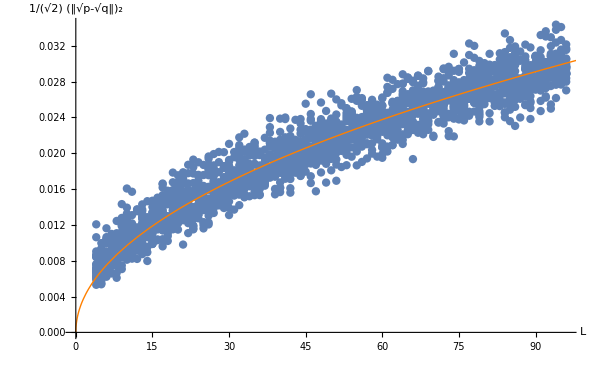

```mathematica
datastream=1; (*1=Hellinger, 2=D(ϕest||ϕ)*)
t=Flatten[Table[{l,data⟦k,l,datastream⟧},{k,kmax},{l,lmin,lmax-lmin}],1];
FindFit[t,a √x,{a},x]
f=(a √x/.%);
plot1=Plot[f,{x,0,100},PlotStyle->{Thick,Orange},ImageSize->600];
plot2=ListPlot[t,PlotRange->{{0,All},{0,All}},ImageSize->600,AxesLabel->{"L","1/(√2)" Subscript[DoubleBracketingBar["√p-√q"], 2]},AxesStyle->16];
plot3=Show[plot2,plot1]
```

{a→0.0497105}

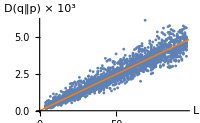

```mathematica
datastream=2; (*1=Hellinger, 2=D(ϕest||ϕ)*)
t=Flatten[Table[{l,10^3 data⟦k,l,datastream⟧},{k,kmax},{l,lmin,lmax-lmin}],1];
FindFit[t,a x,{a},x]
f=(a x/.%);
plot4=Plot[f,{x,0,100},PlotStyle->{Thick,Orange},ImageSize->200];
plot5=ListPlot[t,PlotRange->{{0,All},{0,All}},ImageSize->200,AxesLabel->{"L","D(q‖p) × 10^3"},AxesStyle->16];
plot6=Show[plot5,plot4]
```

```mathematica
Show[plot3,Epilog->Inset[plot6,Scaled[{.73,.08}],Scaled[{.3,0.0}],{45,45}]]
```

-Graphics-

### Average error rate vs. L

```mathematica
(* Return the Hellinger Distance between the true and estimated distributions. *)
AvgErrorRate[n_,L_,err_]:=Module[{ϕ},
ϕ=Fix[Table[GenerateP[n,err],{L-n+1}]];
Return[1-Pr[0,ϕ]];
];
```

{24.7574,Null}

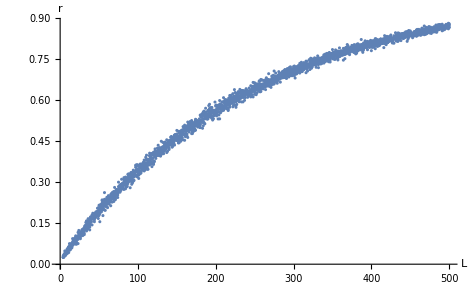

```mathematica
n=2;
err=0.02;
(*spam=0.1; ϵ=0.011; δ=0.05;*)
kmax=5; 
Lmin=4; Lmax=500; Lstep=1;
Lvals=Range[Lmin,Lmax,Lstep];
LL=Length[Lvals];
data=ConstantArray[0,{kmax,Length[Lvals]}];
SetSharedVariable[data,Lvals,l,k,n,err,Lvals];
AbsoluteTiming[
Parallelize[
For[l=1,l≤LL,l++,
For[k=1,k≤kmax,k++,
data⟦k,l⟧=AvgErrorRate[n,Lvals⟦l⟧,err];
];
];
]
]
(*
AbsoluteTiming[
data=ParallelTable[AvgErrorRate[n,Lvals⟦l⟧,err],{k,kmax},{l,LL}];
]
*)

t=Flatten[Table[{Lvals⟦l⟧,data⟦k,l⟧},{k,kmax},{l,LL}],1];
plot3=ListPlot[t,PlotRange->{{0,All},{0,All}},ImageSize->400,AxesLabel->{"L","r"},AxesStyle->20]
```

### Sampling from ϕ and correlation structure.

```mathematica
L=72; n=2; err=0.02; perturb=.01;
ϕ=Fix[Table[GenerateP[n,err],{L-n+1}]];
ϕ=Fix[Table[GenerateAlmostIndependentP[n,err,perturb],{L-n+1}]];
samp:=ChainSample[ϕ];
kmax=2000;
t=Tr/@Ceiling[ParallelTable[samp,{kmax}]/4];
```

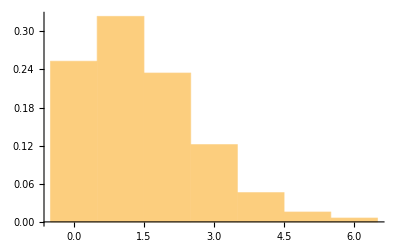

```mathematica
Histogram[t,{Range[0,Max[t]]-1/2},"Probability"]
```

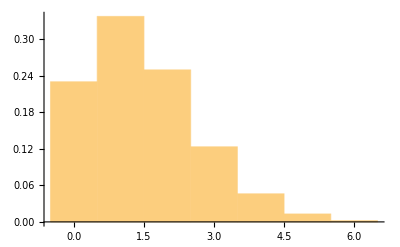

```mathematica
s=RandomVariate[BinomialDistribution[L,Mean[t]/L],kmax];
Histogram[s,{Range[0,Max[s]]-1/2},"Probability"]
```

```mathematica
M2=Table[Partition[NNMarginal[{1,2}+s,ϕ],4],{s,0,L-2}];
M1=Total[#,{1}]&/@M2;
M1=Prepend[M1,Total[M2⟦1⟧,{2}]];
```

```mathematica
Mean[M2]
```

{{0.980944,0.00137643,0.00127809,0.00113773},{0.00135483,0.00134267,0.00109149,0.00145738},{0.00119598,0.00125612,0.00108262,0.00119758},{0.00131896,0.00124559,0.00129781,0.00142265}}

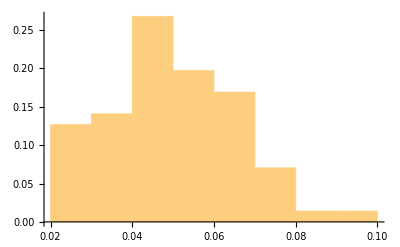

```mathematica
Histogram[MutualInformation/@M2,Automatic,"Probability"]
```

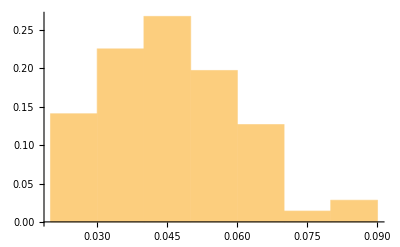

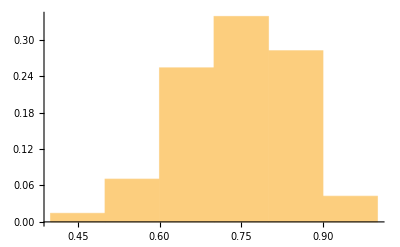

```mathematica
w=Wt[ϕ];
MutualInformation/@w;
Histogram[%,Automatic,"Probability"]
WtCorrelation/@w;
Histogram[%,Automatic,"Probability"]
```

```mathematica
L=72; n=2; err=0.02; perturb=0.01;
ϕ=Fix[Table[GenerateAlmostIndependentP[n,err,0],{L-n+1}]];
ψ=Fix[Table[GenerateP[n,err],{L-n+1}]];
ChainEntropy[ϕ]
ChainEntropy[ψ]
ChainRelativeEntropy[ϕ,ψ]
(*ParallelSum[Pr[x,ϕ] Log2[Pr[x,ϕ]/Pr[x,ψ]],{x,0,4^L-1}]*)
```

12.4661

4.82607

6.19429